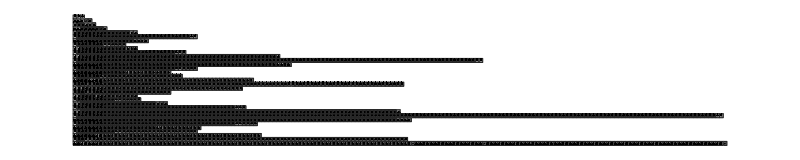

```mathematica
TMToTS[tm_]:=Union[Flatten[tm/.({m_,k_}->{mp_,kp_,dir_}):>{a[m]->{a[m,1],a[m,0]},b[m]->{b[m,1],b[m,0]},c[m]->{c[m,1],c[m,0]},d[m]->{d[m,1],d[m,0]},If[dir==1,{a[m,k]->{a[mp],a[mp]},b[m,k]->{b[mp],b[mp],b[mp],b[mp]},If[kp==1,{If[k==1,{c[m,k]->{b[mp],b[mp],c[mp]}},{c[m,k]->{b[mp],b[mp],c[mp],c[mp]}}]},{If[k==1,{c[m,k]->{c[mp]}},{c[m,k]->{c[mp],c[mp]}}]}],d[m,k]->{d[mp]}},{If[k==1,{a[m,k]->{a[mp]}},{a[m,k]->{a[mp],a[mp]}}],b[m,k]->{b[mp]},If[kp==1,{c[m,k]->{c[mp],c[mp],d[mp],d[mp]}},{c[m,k]->{c[mp],c[mp]}}],d[m,k]->{d[mp],d[mp],d[mp],d[mp]}}]}]];

TagSystemEvolveList[rules_,init_,t_]:=NestList[Drop[Join[#,First[#]/.rules],2]&,init,t];

CompTMTagSystemGraphic[hist_,stot_]:=Graphics[MapIndexed[With[{pos={#2[[2]],-#2[[1]]}},{{EdgeForm[GrayLevel[.15]],GrayLevel[<|a->.8,b->.2,c->.6,d->.4|>[Head[#1]]],Rectangle[pos]},With[{coord=pos+.5,rot=({{Cos[#1],Sin[#1]},{-Sin[#1],Cos[#1]}}&)[N[(2 (#1[[1]]-1) π)/stot]],r=0.18},{Black,Disk[coord,r],If[#1[[1]]>0,Polygon[(coord+rot.#1&)/@{{r,0},{-r,0},{0,.6},{r,0}}],{}]}]}]&,hist,{2}],ImageSize->800];

CompTMTagSystemGraphic[Cases[TagSystemEvolveList[TMToTS[{{1,0}->{3,1,-1},{1,1}->{2,0,1},{2,0}->{1,1,1},{2,1}->{3,1,1},{3,0}->{2,1,1},{3,1}->{1,0,-1}}],{a[1],a[1],c[1]},1500],{a[_],___}],3]
```